```mathematica
g=9.8(*grav. constant*)
(*vter = Sqrt[m g/c]*)
V = 50
th = 40*Pi/180
sol = With[{vter=50}, NDSolve[{x''[t]==(-g x'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2],y''[t] ==-g (1+(y'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2]), {y[0] == 2, x[0] ==0}, {y'[0] == V Sin[th],x'[0] ==V Cos[th]}}, {x,y}, {t,0,200}]]
```

9.8

50

(2 π)/9

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

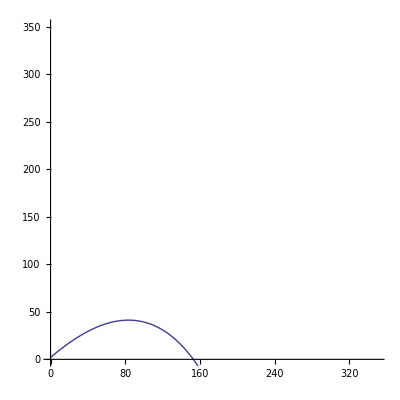

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200}, PlotRange-> {0,350}]
```

```mathematica
Manipulate[
Module[
{sol = NDSolve[{x''[t]==(-g x'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2],y''[t] ==-g (1+(y'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2]), {y[0] == 2, x[0] ==0}, {y'[0] == V Sin[th],x'[0] ==V Cos[th]}}, {x,y}, {t,0,200}]},
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tf}, PlotRange-> {0,350}]],
{{V, 20, "Initial Velocity (m/s)"}, 20,100, Appearance -> "Labeled"},
{{vter,30,"Terminal Velocity (m/s)"},30,100,Appearance->"Labeled"},{{th,.1,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,0.01,"time elapsed (s)"},0.01,18.,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Module[
{sol = NDSolve[{x''[t]==(-g x'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2],y''[t] ==-g (1+(y'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2]), {y[0] == 2, x[0] ==0}, {y'[0] == V Sin[th],x'[0] ==V Cos[th]}}, {x,y}, {t,0,200}]},
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tf}, PlotRange-> {0,350}]],
{{V, 20, "Initial Velocity (m/s)"}, 20,100, Appearance -> "Labeled"},
{{vter,30,"Terminal Velocity (m/s)"},30,100,Appearance->"Labeled"},{{th,.1,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,0.01,"time elapsed (s)"},0.01,18.,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Module[
{sol = NDSolve[{x''[t]==(-g x'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2],y''[t] ==-g (1+(y'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2]), {y[0] == y0, x[0] ==0}, {y'[0] == V Sin[th],x'[0] ==V Cos[th]}}, {x,y}, {t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}/.sol], {V Cos[th] t, y0 + V Sin[th] t -.5 g t^2}},{t,0,tf}, PlotRange-> {0,1000}]],
{{y0, 0, "Initial Height (m)"}, 0,100, Appearance -> "Labeled"},
{{V, 20, "Initial Velocity (m/s)"}, 20,100, Appearance -> "Labeled"},
{{vter,30,"Terminal Velocity (m/s)"},30,100,Appearance->"Labeled"},{{th,.1,"init1ial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,0.01,"time elapsed (s)"},0.01,25.,Appearance->"Labeled"}]
```

```mathematica
m = 6
A = 9.9*10^-3
vter == Sqrt[2 m g/(C R A)]
```